```mathematica
<<PolarDensity.m
r=10;
PolarDensityPlot[(50+Sum[(R/r)^k*100/(Pi*k)*(1+(-1)^(k+1))*Sin[k*theta],{k,1,100}]),{R,0,r},{theta,0,2Pi},PlotPoints->100,ColorFunction -> ColorData["TemperatureMap"]]
```

-Graphics-

```mathematica
r=10;

PolarDensityPlot[400/Pi Sum[1/k(R/r)^(4k)Sin[4*k*theta],{k,1,73,2}],{R,0,r},{theta,0,Pi/4},PlotPoints -> 150,ColorFunction -> ColorData["TemperatureMap"]]
```

-Graphics-

1

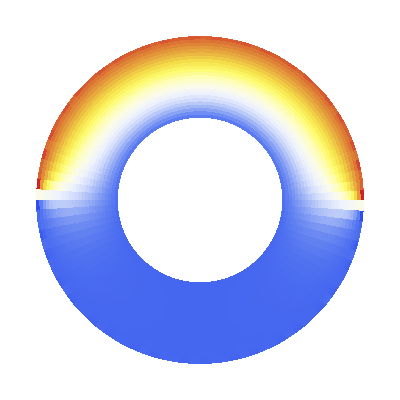

(50 Log[R])/Log[2]+1/π 200 ((2 (-1/R+R) Sin[theta])/(3 n)+(8 (-1/R^3+R^3) Sin[3 theta])/(63 n)+(32 (-1/R^5+R^5) Sin[5 theta])/(1023 n)+(128 (-1/R^7+R^7) Sin[7 theta])/(16383 n)+(512 (-1/R^9+R^9) Sin[9 theta])/(262143 n)+(2048 (-1/R^11+R^11) Sin[11 theta])/(4194303 n)+(8192 (-1/R^13+R^13) Sin[13 theta])/(67108863 n)+(32768 (-1/R^15+R^15) Sin[15 theta])/(1073741823 n)+(131072 (-1/R^17+R^17) Sin[17 theta])/(17179869183 n)+(524288 (-1/R^19+R^19) Sin[19 theta])/(274877906943 n))

```mathematica
r2=2;
r1=1
PolarDensityPlot[50*Log[R]/Log[r]+200/Pi(Sum[(R^k-R^(-k))/(k(r2^k-r2^(-k)))*Sin[k*theta],{k,1,40,2}]),{R,r1,r2},{theta,0,2Pi},PlotPoints->25,ColorFunction -> ColorData["TemperatureMap"]]
```

```mathematica
Table[Cos[n*Pi],{n,0,10}]
```

{1,-1,1,-1,1,-1,1,-1,1,-1,1}

```mathematica
l=10
Manipulate[Plot[Sum[E^(-n^2/l^2*t)*400/(Pi*n)*Sin[n*Pi/l*x],{n,1,200,2}],{x,0,l}],{t,.1,20}]
```

10

```mathematica
Integrate[x*Sin[k*x],x]
```

-(x Cos[k x])/k+Sin[k x]/k^2

```mathematica
l=100
Manipulate[Plot[∑_(n=1)^50 (ⅇ^(-(π^2 n^2 t)/l^2)*(-100  sin((π n x)/l))/(π n))+(100 (l-x))/l,{x,0,l}],{t,0,10000}]
```

100

```mathematica
l=100
Manipulate[Plot[100/l*(l-x)+Sum[E^(-(n^2*Pi^2t/l^2))200/(n*Pi)*(-1)^(n+1)*Sin[n*Pi*x/l],{n,1,400,2}],{x,0,l}],{t,0,10000}]
```

100

```mathematica
2/l Integrate[100/l x Sin[n*Pi*x/l],{x,0,l}]
```

-(200 (n π Cos[n π]-Sin[n π]))/(n^2 π^2)

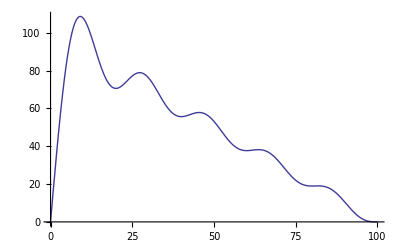

```mathematica
Plot[Sum[200/(n*Pi)*Sin[n*Pi*x/l],{n,1,10}],{x,0,l}]
```